```mathematica
Quit[];
```

## Load the package

```mathematica
<<TRQS`
```

Package TRQS version 0.2.0 (last modification: 07/05/2012).

INFO: Using QRNG (https://qrng.physik.hu-berlin.de/) as a source of randomness.

Note: You have to use QRNGSetCredentials function to provide login information required to use this backend.

## Setup used backend (QRNG)

```mathematica
?QRNGSetCredentials
```

QRNGSetCredentials[user, pass] sets the username and the password used for connecting with the QRNG service (https://qrng.physik.hu-berlin.de/). This function must be used prior of using any functionality of the QRNG backend.

```mathematica
QRNGSetCredentials["???????","???????"] (* provide loginf information for the QRNG service *)
```

User name and password for using QRNG service set!

## Integer numbers

```mathematica
?TrueRandomInteger
```

TrueRandomInteger[{i_min,i_max}] returns a random integer in the range [i_min,i_max].
TrueRandomInteger[{i_min, i_max}, dim] returns a list of random integers in the range [i_min, i_max] with dim elements.
TrueRandomInteger[i] returns a random integer in the range [0,i].
TrueRandomInteger[] returns 0 or 1.

```mathematica
{TrueRandomInteger[],TrueRandomInteger[10],TrueRandomInteger[{10,20}], TrueRandomInteger[{10,20},10]}
```

{0,5,16,{11,17,14,17,14,14,20,15,14,10}}

## Real numbers

```mathematica
?TrueRandomReal
```

TrueRandomReal[{x_min,x_max}] returns a random double in the range [x_min,x_max].
TrueRandomReal[{x_min,x_max}, dim] returns a list of random double in the range [x_min,x_max] with dim elements.
TrueRandomReal[i] returns a random double in the range [0,x].
TrueRandomReal[] returns a random double in the range [0,1].

```mathematica
{TrueRandomReal[],TrueRandomReal[10],TrueRandomReal[{10,20}],TrueRandomReal[{10,20},10]}
```

{0.528959,0.832256,17.6074,{15.34,10.1428,19.9979,11.3748,15.3789,16.2558,11.1776,15.8143,18.8866,10.5959}}

## Normal distribution

```mathematica
?TrueRandomRealNormal
```

TrueRandomRealNormal[m,s,dims] provides a sample of random numbers distributed according to the normal distribution N[m,s] in an array of dimensions given by dims.

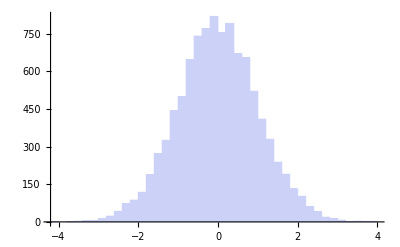

```mathematica
Histogram[Flatten[TrueRandomRealNormal[0,1,{10000}]]]
```

## Ginibre matrix

```mathematica
?TrueGinibreMatrix
```

TrueGinibreMatrix[m,n] returns (m x n)-dimensional complex matrix with entries having real and complex parts distributed according to the normal distribution N[0,1].

```mathematica
TrueGinibreMatrix[10,10]
```

{{-0.761438-1.34872 ⅈ,-0.0447898+0.107108 ⅈ,-1.47566+0.119418 ⅈ,-0.660035+1.6949 ⅈ,-0.416838-0.944123 ⅈ,-1.79342-1.91096 ⅈ,-1.48875-1.48446 ⅈ,0.87538+0.47314 ⅈ,-0.00189135-0.311923 ⅈ,-1.47134-0.403318 ⅈ},{0.411671-2.32073 ⅈ,-1.29335+0.0991637 ⅈ,-0.156733+0.273415 ⅈ,0.888407-1.03815 ⅈ,0.373674-0.27413 ⅈ,-0.672945+0.649271 ⅈ,-0.600049+0.344965 ⅈ,-1.01193-0.615397 ⅈ,-1.12849-0.53745 ⅈ,0.955207-1.50907 ⅈ},{0.619559-0.0698487 ⅈ,-0.356936-0.67779 ⅈ,-1.30946+0.689404 ⅈ,-0.339484+1.03166 ⅈ,0.95333+0.0012537 ⅈ,1.16826+1.43492 ⅈ,-0.853046+0.53772 ⅈ,0.258008+1.26089 ⅈ,0.728349+0.402949 ⅈ,2.04266+0.859115 ⅈ},{0.87927+0.259314 ⅈ,0.993683+0.114907 ⅈ,0.204067+0.219121 ⅈ,-0.180153-0.999653 ⅈ,0.270563-1.90951 ⅈ,-0.880086+0.665663 ⅈ,-0.635806-0.937273 ⅈ,0.197703+1.45254 ⅈ,0.420279+0.930728 ⅈ,-1.12869-1.2878 ⅈ},{0.146985-0.44571 ⅈ,-0.965789-0.236002 ⅈ,1.85639-2.78444 ⅈ,1.36213-0.717345 ⅈ,0.461256-0.415766 ⅈ,0.61835-1.8399 ⅈ,0.216544+0.396304 ⅈ,-0.129708-0.48397 ⅈ,1.15517+1.01985 ⅈ,2.39549+1.65288 ⅈ},{1.30972+0.187406 ⅈ,-0.890972+0.211487 ⅈ,1.70459+1.43076 ⅈ,0.32751+0.853065 ⅈ,2.1846-0.862849 ⅈ,0.0315459-1.92106 ⅈ,-0.924944-0.583009 ⅈ,-1.03906-0.0313297 ⅈ,-0.351857+1.16193 ⅈ,0.857977-0.66979 ⅈ},{-0.220905-1.33572 ⅈ,-2.02729-0.239029 ⅈ,0.267157+0.454309 ⅈ,-0.163909+0.422993 ⅈ,-0.649743+1.74331 ⅈ,-0.084161+0.775128 ⅈ,-1.36585+0.226596 ⅈ,0.664777+2.53384 ⅈ,1.17843+0.666081 ⅈ,0.341783+0.338388 ⅈ},{-1.95653+0.681011 ⅈ,-0.844317-0.988954 ⅈ,-0.957236-0.282097 ⅈ,-0.293704-0.381811 ⅈ,1.08133+0.217722 ⅈ,-1.32801+0.0697123 ⅈ,0.506351-2.91966 ⅈ,0.601191+0.532623 ⅈ,-0.166981-1.51947 ⅈ,1.60319-0.765704 ⅈ},{0.229151+0.915985 ⅈ,0.161856+2.11793 ⅈ,-0.50165-0.694891 ⅈ,-0.864427+0.485718 ⅈ,-1.04678+1.6627 ⅈ,1.41477+1.63169 ⅈ,-0.0311564-0.173991 ⅈ,0.596974+1.0292 ⅈ,-0.648618-0.0778899 ⅈ,1.4574-1.88312 ⅈ},{0.0330205+0.275651 ⅈ,-0.913461-2.00004 ⅈ,-0.125045-0.0974887 ⅈ,-0.683087+1.50036 ⅈ,-0.558881-1.2292 ⅈ,1.34505+0.16796 ⅈ,1.15585-0.0196113 ⅈ,1.06649-0.439862 ⅈ,-1.93797-0.795392 ⅈ,2.04179+0.941368 ⅈ}}

## Random states - HS measure

```mathematica
statesHS=Table[TrueRandomStateHS[4],{2000}];
```

```mathematica
sortedEvalsHS=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesHS]]ᵀ;
```

```mathematica
masterplotHS=Histogram[{sortedEvalsHS[[1]],sortedEvalsHS[[2]],sortedEvalsHS[[3]],sortedEvalsHS[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15];
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-hs-trqs.pdf",masterplotHS];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-hs-trqs.pdf lambda-prob-hs-trqs.eps"];
```

## Random states - Bures measure

```mathematica
statesBures=Table[TrueRandomStateBures[4],{1000}];
```

```mathematica
sortedEvalsBures=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesBures]]ᵀ;
```

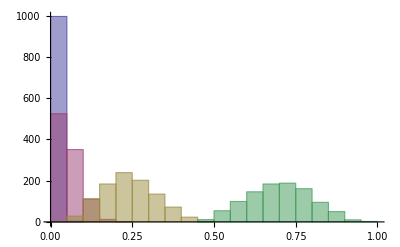

```mathematica
Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]}]
```

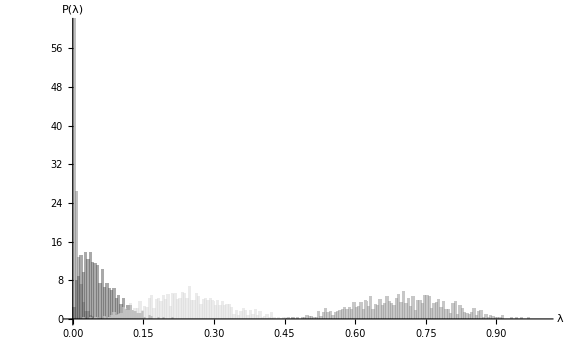

```mathematica
masterplotBures=Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15]
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-bures-trqs.pdf",masterplotBures];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-bures-trqs.pdf lambda-prob-bures-trqs.eps"];
```

## libQuantis configuration

```mathematica
QuantisGetLibVersion[]
```

2.5

```mathematica
QuantisGetSerialNumber[]
```

080259A410